## Developing Packages

## Learning Objectives

### Developing Packages

Understand the differences between packages and notebooks

Learn to load packages

Utilize contexts and namespaces to localize symbols

Write usage messages for functions included in a package

Create a package using the correct sequence of commands

Organize the components of your package with the correct folder structure

Set up autoloading for packages and other definitions

Compare and contrast packages and paclets

## Packages versus Notebooks

### Notebooks (.nb)

Some advantages of using notebooks are:

Ease of use

Support for powerful graphics and interactivity

Ease of editing

However, notebooks can be difficult to distribute.

### Packages (.m or .wl)

Packages provide a way to bundle together new functions. They make them:

Convenient to distribute

Easy to load

Possible to abstract the implementation from the user

## Loading a Package

Wolfram Language is an extensible system, allowing for users to add in more functionality. Packages can be used to put together a collection of new Wolfram Language function definitions that can be "taught" to Wolfram Language.

Packages can vary in size from a handful of functions to several hundred. No matter their size, they can be accessed in the same way.

You can explicitly tell Wolfram Language to read in a package at any point using Get:

```mathematica
Get["package file path"]
```

Or:

```mathematica
<<PackageNameHere`
```

This reads in a sample package:

```mathematica
<<ExampleData/Collatz.m
```

```mathematica
Collatz[4]
```

{4,2,1}

You can also set it up so that a particular package is read in only if it is needed, using Needs:

```mathematica
Needs["DatabaseLink`"]
```

The default location to look for packages is the current working directory (found using the function Directory):

```mathematica
Directory[]
```

You can get a list of the contexts corresponding to all packages that have been loaded in your current Wolfram System session:

```mathematica
$Packages
```

## Namespaces

### Context

Context allows definitions of functions to be separated into appropriate groupings, each with a unique identifier.

The current context can be found using:

```mathematica
$Context
```

Global`

```mathematica
x=10
```

10

```mathematica
Context[x]
```

Global`

To start a new context, the function Begin is required, along with the name of the context you wish to start.

To end the context, End is used. This will automatically end the last context that was started:

```mathematica
$Context
```

Global`

```mathematica
Begin["myContext1`"]
```

myContext1`

```mathematica
$Context
```

myContext1`

```mathematica
yy=20
```

20

```mathematica
Context[yy]
```

myContext1`

```mathematica
End[]
```

myContext1`

```mathematica
$Context
```

Global`

The Context function gives the context in which a symbol appears:

```mathematica
Context[Plus]
```

System`

Functions defined in a specific context are not available for use outside the context right away.

You can use the function within the open context:

```mathematica
Begin["Demo`"];
cube::usage="This function takes an integer and cubes it";
cube[x_Integer]:=x^3;

cube[4]
End [];
```

64

You can also call a function outside its context using the absolute context path:

```mathematica
Demo`cube[4]
```

64

### Context Path

One of the easiest methods of accessing a function from another context is to add the context to the context path:

```mathematica
AppendTo[$ContextPath,"Demo`"]
```

{DocumentationSearch`,ResourceLocator`,URLUtilities`,PacletManager`,System`,Global`,Demo`}

```mathematica
cube[10]
```

1000

The context path is the list of locations (in order) that Wolfram Language will look through for the definitions of functions. The current list can be accessed using the global variable. Be aware that if a definition for a function exists in more than one context, then the order of the context path matters:

```mathematica
$ContextPath
```

{DocumentationSearch`,ResourceLocator`,URLUtilities`,PacletManager`,System`,Global`}

Once a package is loaded, it is automatically added to the end of the context path, allowing a user to use the functions from that context without having to use an absolute context path.

## Usage Messages

### Provide Information

All built-in functions have usage messages, which can be found when you use the Information function:

```mathematica
?Plus
```

This behavior can be recreated using the message functionality built in:

```mathematica
f::usage = "f[n] prints n asterisks";
```

```mathematica
?f
```

Not all messages are usage messages, but they all follow the pattern:

```mathematica
Symbol::tag
```

All messages belong to a specific symbol. The tag comes after the :: (MessageName). The tag is used to provide a name for the message.

Process messages can be generated during an evaluation. For example, argx is used to report an incorrect number of arguments:

```mathematica
Message[f::argx,"Function f",2]
```

f::argx: Function f called with 2 arguments; 1 argument is expected.

Define a function that issues an error message:

```mathematica
f[n_]:=StringRepeat["*",If[n<=80,n,Message[f::len,n];80]]
```

Define the message:

```mathematica
f::len = "Argument `1` is too large; limiting to 80";
```

```mathematica
f[20]
```

********************

```mathematica
f[100]
```

f::len: Argument 100 is too large; limiting to 80

********************************************************************************

Messages gives a list of the messages associated with a function:

```mathematica
Messages[f]
```

{HoldPattern[f::argx]:>`1` called with `2` arguments; 1 argument is expected.,HoldPattern[f::len]:>Argument `1` is too large; limiting to 80,HoldPattern[f::usage]:>f[n] prints n asterisks}

### Making the Symbol or Function Available for Use

Including the usage message outside the Private context in a package allows the function to be explicitly accessed in the context of the packages. Functions defined within the private context without a usage message outside the private context are not available for use outside the package.

## Syntax Coloring and Other Advisories

SyntaxInformation is a function that defines what pattern of arguments is acceptable. This is so that any other pattern of arguments will result in the front end display alerting the user they have provided too many or too few arguments:

```mathematica
ClearAll[f]
```

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_,_}};
```

```mathematica
{f[],f[x],f[x,y],f[x,y,z],f[x,y,z,w]};
```

SyntaxInformation is also usable with options:

```mathematica
SyntaxInformation[f]={"ArgumentsPattern"->{_,_,OptionsPattern[]}};
```

```mathematica
f[x,y,aab->2,aaa->3,bba->4];
```

## Editing a Package

You can create and edit a package file using the package editor in Mathematica (File ▶ New ▶ Package/Script ▶ Wolfram Language Package).

The syntax for creating a new package is simple, using the BeginPackage function, the name of the package and a backtick:

```mathematica
BeginPackage["NewPackage`"]
```

Your package may have dependencies on other packages; these should also be included in the definition. It can be done within the BeginPackage function at the beginning or can be included using the Needs function within the package:

```mathematica
BeginPackage["NewPackage`",{"OldPackage`"}]
```

```mathematica
Needs["OldPackage`"]
```

You can start and end a context within a package using Begin and End.

Use the EndPackage function to end the definition of a package:

```mathematica
EndPackage[]
```

There is a standard sequence of Wolfram Language commands that is typically used to set up the contexts in a package:

```mathematica
Grid[{
{Style["BeginPackage[\"Package`\"]","Input"],Style["set Package` to be the current context,and put only System` on the context search path","Text"]},{Style["f::usage=\"text\",…","Input"],Style["introduce the objects intended for export (and no others)","Text"]},{Style["Begin[\"`Private`\"]","Input"],Style["set the current context to Package`Private`","Text"]},
{Style["f[args]=value,…","Input"],Style["give the main body of definitions in the package","Text"]},
{Style["End[]","Input"],Style["revert to the previous context (here Package`)","Text"]},
{Style["EndPackage[]","Input"],Style["end the package,prepending the Package` to the context search path","Text"]}
},Alignment->Left]
```

BeginPackage["Package`"] | set Package` to be the current context,and put only System` on the context search path
f::usage="text",… | introduce the objects intended for export (and no others)
Begin["`Private`"] | set the current context to Package`Private`
f[args]=value,… | give the main body of definitions in the package
End[] | revert to the previous context (here Package`)
EndPackage[] | end the package, prepending the Package` to the context search path

## Package Folder Structure

Mathematica has the ability to handle stylesheets for document-wide formatting and palettes as additional tool windows. To start with, some Wolfram-defined ones are included; you may, however, wish to create your own. Once this is done, they need to be placed in the appropriate folder for them to be picked up by Mathematica.

The base directory for all resources can be found using the global variable. Then navigate into the Applications folder:

```mathematica
$UserBaseDirectory
```

The structure of this folder and any packages should be as follows:

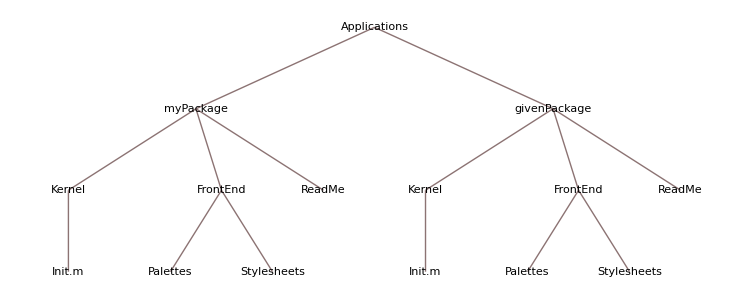

```mathematica
TreeForm["Applications" [ "myPackage" ["Kernel"[ "Init.m"],"FrontEnd" ["Palettes", "Stylesheets"] ,"ReadMe"],"givenPackage" ["Kernel"[ "Init.m"],"FrontEnd" ["Palettes", "Stylesheets"] ,"ReadMe"] ] ]
```

All .nb files in Palettes and Stylesheets appear on appropriate menus, and the stylesheet will be on the path for StyleDefinitions→"stylesheets.nb" once the package folder has been placed in the correct directory (a restart of Mathematica may be needed).

## Autoloading

It is possible to get Mathematica to automatically start with packages loaded, variables initialized or data already imported. This can be done through the use of the InitializationValue function and the $Initialization global variable.

By default, $Initialization is empty:

```mathematica
InitializationValue[$Initialization]
```

{}

Now set up a package to autoload:

```mathematica
InitializationValue[$Initialization]=Hold[Get["ComputerArithmetic`"]]
```

Hold[<<ComputerArithmetic`]

```mathematica
Ulp[1000.]
```

1.13687×10^-13

Or set a variable to contain some data:

```mathematica
{xNew,yNew,zNew}
```

{10,20,30}

```mathematica
InitializationValue[$Initialization]=Hold[{xNew=10,yNew=20,zNew=30}]
```

Hold[{xNew=10,yNew=20,zNew=30}]

To stop this behavior, just use the Remove function:

```mathematica
Remove[InitializationValue[$Initialization]];
```

```mathematica
InitializationValue[$Initialization]
```

WARNING : This cannot be used with any code that generates dialog boxes or requires user input (e.g. login).

## Package versus Paclet

### Package File

A package file is:

A simple .m or .wl file

Easily installed using Get (so package need not be explicitly installed)

Simple and straightforward to use, but can become cumbersome if packed with too many functions

### Paclet

A "paclet" in Wolfram Language is more like what is called a "package" in other programming languages.

A paclet:

Is an archive bundling together packages (i.e. .wl or .m files) containing new functions, stylesheets, palettes, documentation notebooks or data files all in a single .paclet file along with metadata

Makes it easy to install multiple resources at once (user does not need to know the details about the individual package files or load/install them one by one)

Allows for automatic updates

Is the "Wolfram" way to implement packages and distribute

Many built-in Wolfram Language functions and data resources are implemented and maintained using paclets:

```mathematica
PacletObject["ExternalEvaluate"]["Properties"]
```

{Name,Version,WolframVersion,Qualifier,SystemID,ProductID,Extensions,Description,Category,Keywords,BuildNumber,UUID,Creator,Publisher,URL,Support,Internal,AssetLocation,Context,Loading,AutoUpdating,Enabled,Location,PacletInfo}

```mathematica
PacletObject["ExternalEvaluate"]["Location"]
```

/Applications/Mathematica.app/Contents/SystemFiles/Components/ExternalEvaluate

```mathematica
Dataset@FileSystemMap[Hyperlink[FileNameTake[#],#]&,Information[PacletObject["ExternalEvaluate"],"Location"],Infinity]
```

A PacletInfo.wl or PacletInfo.m file containing metadata describing a paclet and its resources is essential for converting a directory or collection of files into a paclet.

### Wolfram Language Paclet Repository

Wolfram offers a curated repository of various paclets at the Wolfram Language Paclet Repository.

For example, you can get a paclet that helps with protein visualization by running the following code:

```mathematica
PacletInstall["WolframChemistry/ProteinVisualization"]
```

PacletObject[…]

After installing the paclet and loading the corresponding context, you can easily use the included functionality:

```mathematica
Needs["WolframChemistry`ProteinVisualization`"]
```

```mathematica
{{-Graphics-, AlphaCarbonPathPlot3D}}["6RB9","BackboneColorRules"->{"Chains",Automatic}]
```

-Graphics3D-

On the off chance that the functionality you need is not already in Wolfram Language, make sure to check the paclet repository (as well as the Wolfram Function Repository!).

#### Tutorial

If you are interested in creating your own paclets, please see the tutorial linked on the Wolfram Language Paclet Repository page.

## Using IDEs for Wolfram Language Development

There are several IDEs available to help you develop your Wolfram Language projects.

#### Workbench

Eclipse-based IDE for Wolfram Language

#### VS Code

Wolfram System Integration with Visual Studio Code

#### Sublime

Official Sublime Text Package for Wolfram Language

#### Talk and Workshop from Wolfram Technology Conference

Developing Wolfram Language Code in Other Editors and IDEs with LSP

## References

Wolfram Language Packages

Setting Up Wolfram Language Packages

Package Bulletproofing

Robustness & Error Handling

Set Up Error Checking and Messages in a Function

Paclets and Paclet Development